```mathematica
(*s=InputString["Enter xml file name","tooth.xml"]//StringReplace[#," "->""]&;*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_strong_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_weak_red.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_green_1000.xml"];*)
(*xml=Import[NotebookDirectory[]<>"~images\\"<>"nucleon_naive_optimized_red_1000.xml"];*)
xml=Import[NotebookDirectory[]<>"~images\\"<>"foot_naive.xml"];
{tfifile,volumefile,legends,face,imagefilenames,txtfilenames,{featurefilename,visibilityfilename},resultxml,imagefile,rawfile,dataname}=xml;
(*Column[xml,Background->{{Lighter@LightYellow,Lighter@LightBlue}},Frame->True,FrameStyle->Directive[LightGray,Thin,Dashed]]*)

tf=Import[tfifile,"XML"];
bincount=256;
intensity=ToExpression@Cases[tf,XMLElement["intensity",{"value"->atrib_,___},___]:>atrib,∞];
r=ToExpression@Cases[tf,XMLElement["colorL",{"r"->atrib_,___},___]:>atrib,∞];
g=ToExpression@Cases[tf,XMLElement["colorL",{___,"g"->atrib_,___},___]:>atrib,∞];
b=ToExpression@Cases[tf,XMLElement["colorL",{___,"b"->atrib_,___},___]:>atrib,∞];
a=ToExpression@Cases[tf,XMLElement["colorL",{___,"a"->atrib_},___]:>atrib,∞];
rgbcolors=(#/255.&)/@Transpose[{r,g,b}]//(RGBColor/@#&);
rgbfunction=(Blend[Transpose[{intensity,rgbcolors}], #1] & );
rgba=(#/255.&)/@Transpose[{r,g,b,a}]//(RGBColor/@#&);
rgbafunction=(Blend[Transpose[{intensity,rgba}], #1] & );
alpha=(#/255.&)/@a;

d = Import[volumefile,"Image3D"];
colorized=Image3D[d,ColorFunction->rgbafunction];
{lightness,chroma,hue,opacity}=ImageApply[List@@rgbafunction[#]&,d]//Image3D[#,ColorSpace->"RGB"]&//ColorSeparate[ColorConvert[#,"LCH"]]&;
(*lo=ImageMultiply[lightness,opacity];
co=ImageMultiply[chroma,opacity];*)
(*g1=ImageDifference[GaussianFilter[lightness,{2,Sqrt[2]/8.*2}],GaussianFilter[lightness,{4,Sqrt[2]/8.*4}]]
g2=ImageDifference[GaussianFilter[chroma,{2,Sqrt[2]/8.*2}],GaussianFilter[chroma,{4,Sqrt[2]/8.*4}]]
g3=ImageDifference[GaussianFilter[hue,{2,Sqrt[2]/8.*2}],GaussianFilter[hue,{4,Sqrt[2]/8.*4}]];
g4=ImageDifference[GaussianFilter[opacity,{2,Sqrt[2]/8.*2}],GaussianFilter[opacity,{4,Sqrt[2]/8.*4}]];*)
{g1,g2}=ParallelMap[ImageDifference[GaussianFilter[#,{2,Sqrt[2]/8.*2}],GaussianFilter[#,{4,Sqrt[2]/8.*4}]]&,{lightness,chroma}];

pos=intensity[[#]]&/@Flatten@Position[alpha,_?(#==0&)];
index=Flatten@Position[alpha,_?(#>0&)];
features=Table[ImageApply[If[#≥pos[[i]] && #≤pos[[i+1]],1,0]&,d],{i,1,Length[pos],2}];
chartcolors=rgbcolors[[#]]&/@index;
colorizedfeatures=ImageMultiply[colorized,#]&/@features;
viewpoints=<|"top":>Top,"back":>Back,"left":>Left,"bottom":>Bottom,"front":>Front,"right":>Right|>;
MapIndexed[Export[StringReplace[imagefile,"."->"_"<>ToString[First[#2]]<>"."],Show[#,Boxed->False,ViewPoint->viewpoints[face]]]&,colorizedfeatures];

intensity0=intensity;
alpha0=alpha;
rangeOfAlpha=Range[Length[alpha]];
If[First[intensity0]>0,intensity0=Join[{0},intensity0];alpha0=Join[{0},alpha0];rangeOfAlpha+=1];
If[Last[intensity0]<1,intensity0=Join[intensity0,{1}];alpha0=Join[alpha0,{0}]];
(*ListLinePlot[Transpose[{intensity0,alpha0}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
(*fun=Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1];*)
(*Plot[fun[x],{x,0,1},PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"user specified transfer function"]*)
index0=Flatten@Position[alpha0,_?(#>0&)];

targets=<|2->{0.2,0.8},3->{0.1,0.3,0.6},4->{0.1,0.2,0.3,0.4}|>;
target=targets[Length[index0]]
CloseKernels[];
LaunchKernels[8];
Clear[f];
Clear[data];
records={};
```

{0.3,0.7}

```mathematica
top:=Module[{list,count,img,list2,list3,d1},(* top *)
list=Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d1=Image3D[list3]]
back:=Module[{list,count,img,list2,list3,tmp,d2},(* back *)
list=Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left:=Module[{list,count,img,list2,list3,tmp,d3},(* left *)
list=Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom:=Module[{list,count,img,list2,list3,d4},(* bottom *)
list=Reverse@Image3DSlices[data,All,1];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
d4=Image3D[Reverse[list3]]]
front:=Module[{list,count,img,list2,list3,tmp,d5},(* front *)
list=Reverse@Image3DSlices[data,All,2];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right:=Module[{list,count,img,list2,list3,tmp,d6},(* right *)
list=Reverse@Image3DSlices[data,All,3];
count=Length[list];
img=First[list];
list2=Table[img=ImageApply[#1+Clip[1-#1,{0,1}]*f[#2]&,{img,list[[i]]}],{i,2,count}]//Join[{First[list]},#]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,count}]//Join[{First[list]},#]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices=<|"top":>top,"back":>back,"left":>left,"bottom":>bottom,"front":>front,"right":>right|>;
```

```mathematica
top2:=Module[{list,img,list2,list3,df,d1},(* top *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d1=Image3D[list3]
]
back2:=Module[{list,img,list2,list3,tmp,df,d2},(* back *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d2=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
left2:=Module[{list,img,list2,list3,tmp,df,d3},(* left *)
df=ImageApply[f[#]&,data];
list=Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d3=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
bottom2:=Module[{list,img,list2,list3,df,d4},(* bottom *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,1];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
d4=Image3D[Reverse[list3]]]
front2:=Module[{list,img,list2,list3,tmp,df,d5},(* front *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,2];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[list3];
d5=ImageRotate[tmp,{90 Degree,{1,0,0}}]]
right2:=Module[{list,img,list2,list3,tmp,df,d6},(* right *)
df=ImageApply[f[#]&,data];
list=Reverse@Image3DSlices[df,All,3];
img=First[list];
list2=Table[img=ImageAdd[img,ImageMultiply[ImageClip@ColorNegate[img],i]],{i,list[[2;;]]}]//Prepend[#,First[list]]&;
list3=Table[ImageSubtract[list2[[i]],list2[[i-1]]],{i,2,Length[list]}]//Prepend[#,First[list]]&;
tmp=Image3D[Reverse[list3]];
d6=ImageRotate[tmp,{90 Degree,{1,0,0}}]//ImageRotate[#,-90 Degree]&]
renderslices2=<|"top":>top2,"back":>back2,"left":>left2,"bottom":>bottom2,"front":>front2,"right":>right2|>;
```

```mathematica
VisibilitySaliency[peaks_]:=Module[{alpha2,fun,vis,viss,vs,mean,total},
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
Visibility[fun_]:=Module[{vis,viss,vs,mean,total},
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
]
```

```mathematica
(*(* compare the performance of 3 methods for computing visibility-weighted saliency *)
n=10;

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ParallelMap[ImageMultiply[#,vis]&,{g1,g2}];
total=ParallelMap[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=ParallelTable[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=ImageMultiply[g1,vis];(* weighted by lightness DoG (difference of Gaussians) *)
(*vs=Table[ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/ImageMeasurements[viss,"TotalIntensity"],{i,features}];*)
total=ImageMeasurements[viss,"TotalIntensity"];
vs=ParallelTable[If[total≠0,ImageMeasurements[ImageMultiply[viss,i],"TotalIntensity"]/total,0],{i,features}];
viss2=ImageMultiply[g2,vis];(* weighted by chroma DoG *)
(*vs2=Table[ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/ImageMeasurements[viss2,"TotalIntensity"],{i,features}];*)
total2=ImageMeasurements[viss2,"TotalIntensity"];
vs2=ParallelTable[If[total2≠0,ImageMeasurements[ImageMultiply[viss2,i],"TotalIntensity"]/total2,0],{i,features}];
mean=Mean[{vs,vs2}]
],{n}];
Total[#&@@@t]/n

t=Table[AbsoluteTiming[
peaks={0.1,0.3,0.6};
alpha2=alpha0;
MapIndexed[(alpha2[[#]]=peaks[[First@#2]])&,index0];
fun=Interpolation[Transpose[{intensity0,alpha2}],InterpolationOrder->1];
vis=Block[{f=fun,data=d},renderslices2[face]];
viss=Map[ImageMultiply[#,vis]&,{g1,g2}];
total=Map[ImageMeasurements[#,"TotalIntensity"]&,viss];
vs=Table[Table[If[total[[j]]≠0,ImageMeasurements[ImageMultiply[viss[[j]],i],"TotalIntensity"]/total[[j]],0],{i,features}],{j,Length[total]}];
mean=Mean[vs]
],{n}];
Total[#&@@@t]/n*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*gradient descent with fixed step size*)
epsilon=0.01;
stepsize=0.05;
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaks0},
mean=Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaks0=peaks;
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
If[t2==0 && rms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks0,rms,steps}
],{iterator,50}];
```

71.635304

37

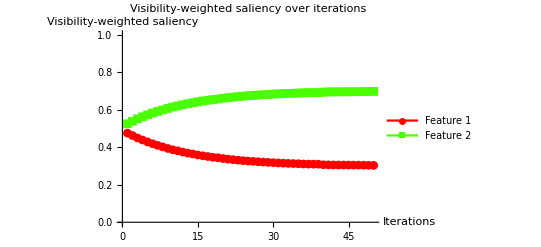

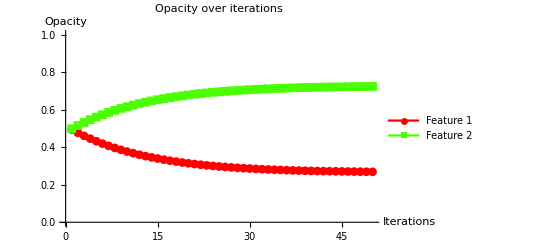

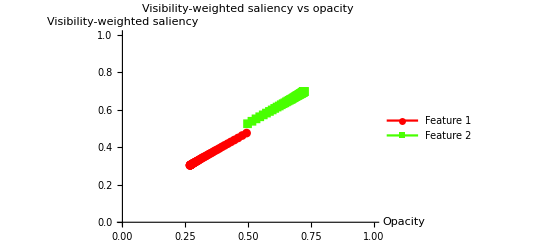

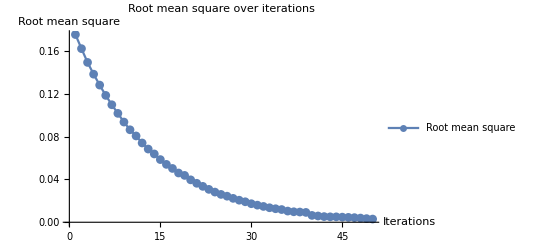

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps
1 | 0.475128
0.524872 | 0.494118
0.498039 | 0.175128 | -0.0175128
0.0175128
2 | 0.461973
0.538027 | 0.476605
0.515552 | 0.161973 | -0.0161973
0.0161973
3 | 0.449134
0.550866 | 0.460408
0.531749 | 0.149134 | -0.0149134
0.0149134
4 | 0.438149
0.561851 | 0.445494
0.546663 | 0.138149 | -0.0138149
0.0138149
5 | 0.427977
0.572023 | 0.431679
0.560478 | 0.127977 | -0.0127977
0.0127977
6 | 0.418353
0.581647 | 0.418882
0.573275 | 0.118353 | -0.0118353
0.0118353
7 | 0.409624
0.590376 | 0.407046
0.585111 | 0.109624 | -0.0109624
0.0109624
8 | 0.401596
0.598404 | 0.396084
0.596073 | 0.101596 | -0.0101596
0.0101596
9 | 0.393485
0.606515 | 0.385924
0.606233 | 0.0934847 | -0.00934847
0.00934847
10 | 0.386268
0.613732 | 0.376576
0.615581 | 0.0862678 | -0.00862678
0.00862678
11 | 0.380529
0.619471 | 0.367949
0.624208 | 0.0805295 | -0.00805295
0.00805295
12 | 0.373967
0.626033 | 0.359896
0.632261 | 0.0739672 | -0.00739672
0.00739672
13 | 0.368297
0.631703 | 0.352499
0.639657 | 0.0682968 | -0.00682968
0.00682968
14 | 0.36373
0.63627 | 0.34567
0.646487 | 0.0637298 | -0.00637298
0.00637298
15 | 0.358467
0.641533 | 0.339297
0.65286 | 0.0584668 | -0.00584668
0.00584668
16 | 0.353995
0.646005 | 0.33345
0.658707 | 0.0539948 | -0.00539948
0.00539948
17 | 0.350207
0.649793 | 0.328051
0.664106 | 0.050207 | -0.0050207
0.0050207
18 | 0.345962
0.654038 | 0.32303
0.669127 | 0.0459622 | -0.00459622
0.00459622
19 | 0.343709
0.656291 | 0.318434
0.673723 | 0.0437092 | -0.00437092
0.00437092
20 | 0.339576
0.660424 | 0.314063
0.678094 | 0.0395762 | -0.00395762
0.00395762
21 | 0.336357
0.663643 | 0.310105
0.682052 | 0.0363566 | -0.00363566
0.00363566
22 | 0.333489
0.666511 | 0.306469
0.685687 | 0.0334889 | -0.00334889
0.00334889
23 | 0.330686
0.669314 | 0.303121
0.689036 | 0.0306855 | -0.00306855
0.00306855
24 | 0.328139
0.671861 | 0.300052
0.692105 | 0.0281393 | -0.00281393
0.00281393
25 | 0.325977
0.674023 | 0.297238
0.694919 | 0.0259769 | -0.00259769
0.00259769
26 | 0.324315
0.675685 | 0.29464
0.697516 | 0.0243146 | -0.00243146
0.00243146
27 | 0.322288
0.677712 | 0.292209
0.699948 | 0.0222881 | -0.00222881
0.00222881
28 | 0.320568
0.679432 | 0.28998
0.702177 | 0.0205684 | -0.00205684
0.00205684
29 | 0.319103
0.680897 | 0.287923
0.704234 | 0.0191034 | -0.00191034
0.00191034
30 | 0.317297
0.682703 | 0.286013
0.706144 | 0.0172975 | -0.00172975
0.00172975
31 | 0.315953
0.684047 | 0.284283
0.707874 | 0.0159531 | -0.00159531
0.00159531
32 | 0.314757
0.685243 | 0.282688
0.709469 | 0.0147568 | -0.00147568
0.00147568
33 | 0.313535
0.686465 | 0.281212
0.710945 | 0.0135351 | -0.00135351
0.00135351
34 | 0.312612
0.687388 | 0.279859
0.712298 | 0.0126118 | -0.00126118
0.00126118
35 | 0.311848
0.688152 | 0.278598
0.713559 | 0.0118479 | -0.00118479
0.00118479
36 | 0.310434
0.689566 | 0.277413
0.714744 | 0.0104338 | -0.00104338
0.00104338
37 | 0.309779
0.690221 | 0.276369
0.715788 | 0.00977865 | -0.000977865
0.000977865
38 | 0.309524
0.690476 | 0.275391
0.716765 | 0.00952379 | -0.000952379
0.000952379
39 | 0.30918
0.69082 | 0.274439
0.717718 | 0.00918047 | -0.000918047
0.000918047
40 | 0.306384
0.693616 | 0.273521
0.718636 | 0.00638433 | -0.000638433
0.000638433
41 | 0.305849
0.694151 | 0.272883
0.719274 | 0.00584891 | -0.000584891
0.000584891
42 | 0.305274
0.694726 | 0.272298
0.719859 | 0.00527367 | -0.000527367
0.000527367
43 | 0.305054
0.694946 | 0.27177
0.720387 | 0.00505377 | -0.000505377
0.000505377
44 | 0.30504
0.69496 | 0.271265
0.720892 | 0.00503974 | -0.000503974
0.000503974
45 | 0.304765
0.695235 | 0.270761
0.721396 | 0.00476509 | -0.000476509
0.000476509
46 | 0.304556
0.695444 | 0.270284
0.721872 | 0.00455648 | -0.000455648
0.000455648
47 | 0.304303
0.695697 | 0.269829
0.722328 | 0.00430328 | -0.000430328
0.000430328
48 | 0.303904
0.696096 | 0.269399
0.722758 | 0.00390402 | -0.000390402
0.000390402
49 | 0.303393
0.696607 | 0.269008
0.723149 | 0.00339314 | -0.000339314
0.000339314
50 | 0.30298
0.69702 | 0.268669
0.723488 | 0.00298006 | -0.000298006
0.000298006

```mathematica
t2-t1
iteration
saliency1=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_fixed.png",saliency1];
opacity1=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_fixed.png",opacity1];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms1=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_fixed.png",rms1];
table1=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_fixed.png",table1];
(*path1=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path1=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path1]}];
```

```mathematica
(*alpha0[[#]]&/@index0
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0]*)
(*(*first order newton*)
target={0.1,0.3,0.6};
stepsize=0.1;
previous={{0,0,0},{0,0,0}};
list=Table[Module[{peaks,mean,steps,rms,f1,f0,diff,square,derivative,xx,dx,yy,df,factor},
mean=visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
derivative=2*(mean-target);
square=(mean-target)^2;
If[Norm[First@previous]>0,{f1,f0,xx,yy}=previous,{f1,f0,xx,yy}={derivative,square,peaks,mean}];
(*diff=mean-y1;
steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,(target-mean)*(peaks-x1)/(mean-y1)*stepsize,2*(target-mean)*stepsize];*)
(*dx=peaks-xx;
df=If[Product[dx[[i]],{i,Length[dx]}]≠0,(mean-yy)/dx,1];*)
(*derivative=derivative*df;*)
diff=derivative-f1;
previous={derivative,square,peaks,mean};
df=If[Product[diff[[i]],{i,Length[diff]}]≠0,-(square-f0)/diff*stepsize,-derivative*stepsize];(*should be second-order but look like first-order*)
dx=-derivative*stepsize;
steps=Table[If[Abs[dx[[i]]]>Abs[df[[i]]],dx[[i]],df[[i]]],{i,Length[mean]}];
(*steps=If[Product[diff[[i]],{i,Length[diff]}]≠0,-derivative*(peaks-xx)/diff*stepsize,-derivative*stepsize];*)
(*steps=-derivative*stepsize;*)
peaks=Clip[peaks+steps,{0,1}];
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
{mean,peaks,rms,steps,dx,df,Table[Abs[df[[i]]]>Abs[dx[[i]]],{i,Length[dx]}]}
],{30}];*)
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*parallel gradient*)
multipliers={1,2,4,8};
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,meanlist,peaklist,rmslist,minindex},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=ParallelMap[Clip[peaks+steps*#,{0,1}]&,multipliers];
meanlist=ParallelMap[VisibilitySaliency[#]&,peaklist];
rmslist=ParallelMap[RootMeanSquare[#-target]&,meanlist];
minindex=First@Ordering[rmslist,1];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=meanlist[[minindex]];
If[t2==0 && rmslist[[minindex]]<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

17.071891

4

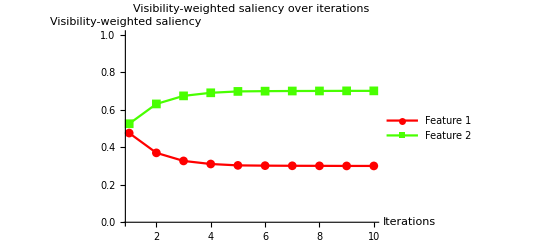

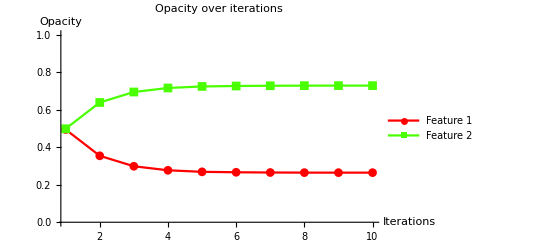

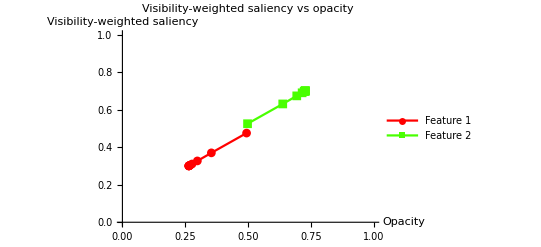

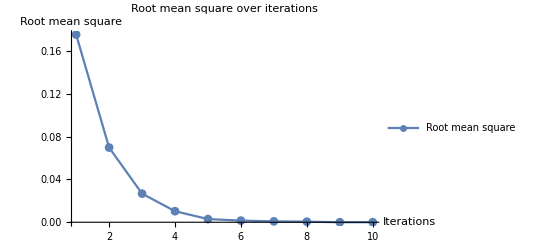

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.475128
0.524872 | 0.494118
0.498039 | 0.175128 | -0.0175128
0.0175128 | 8
2 | 0.369704
0.630296 | 0.354016
0.638141 | 0.0697041 | -0.00697041
0.00697041 | 8
3 | 0.326703
0.673297 | 0.298252
0.693905 | 0.0267031 | -0.00267031
0.00267031 | 8
4 | 0.310319
0.689681 | 0.27689
0.715267 | 0.010319 | -0.0010319
0.0010319 | 8
5 | 0.302959
0.697041 | 0.268635
0.723522 | 0.00295866 | -0.000295866
0.000295866 | 8
6 | 0.301557
0.698443 | 0.266268
0.725889 | 0.001557 | -0.0001557
0.0001557 | 8
7 | 0.300813
0.699187 | 0.265022
0.727135 | 0.000812664 | -0.0000812664
0.0000812664 | 8
8 | 0.300522
0.699478 | 0.264372
0.727785 | 0.000521512 | -0.0000521512
0.0000521512 | 2
9 | 0.30003
0.69997 | 0.264268
0.727889 | 0.0000295581 | -2.95581×10^-6
2.95581×10^-6 | 1
10 | 0.30003
0.69997 | 0.264265
0.727892 | 0.0000295581 | -2.95581×10^-6
2.95581×10^-6 | 1

```mathematica
t2-t1
iteration
saliency2=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_parallelsearch.png",saliency2];
opacity2=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_parallelsearch.png",opacity2];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms2=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_parallelsearch.png",rms2];
table2=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_parallelsearch.png",table2];
(*path2=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path2=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path2]}];
```

```mathematica
(*reset peak control points*)
alpha0[[#]]&/@index0;
peaks=alpha[[#]]&/@index;
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
(*line search*)
previous={0,0,0};
iteration=0;
t1=AbsoluteTime[];
t2=0;
list=Table[Module[{peaks,mean,steps,rms,peaklist,minindex,minrms,minmean,rms2,mean2},
mean=If[Norm[previous]>0,previous,Visibility[Interpolation[Transpose[{intensity0,alpha0}],InterpolationOrder->1]]];
rms=RootMeanSquare[mean-target];
peaks=alpha0[[#]]&/@index0;
steps=-2*(mean-target)*stepsize;
peaklist=Map[Clip[peaks+steps*#,{0,1}]&,multipliers];
minindex=1;
minmean=VisibilitySaliency[peaklist[[minindex]]];
minrms=RootMeanSquare[minmean-target];
Do[mean2=VisibilitySaliency[peaklist[[i]]];
rms2=RootMeanSquare[mean2-target];
If[rms2<minrms,minrms=rms2;minmean=mean2;minindex=i,Return[i]];
,{i,Range[2,4]}];
MapIndexed[(alpha0[[#]]=peaklist[[minindex]][[First@#2]])&,index0];
previous=minmean;
If[t2==0 && minrms<epsilon,t2=AbsoluteTime[];iteration=iterator];
{mean,peaks,rms,steps,multipliers[[minindex]]}
],{iterator,10}];
```

32.406178

4

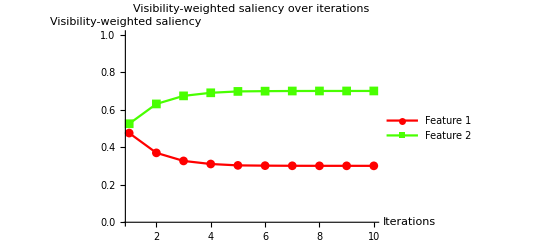

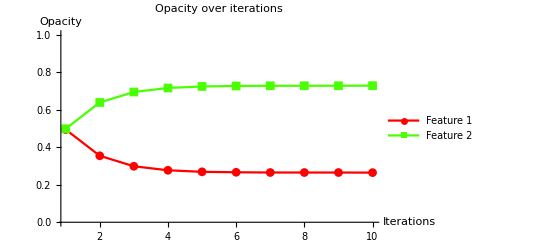

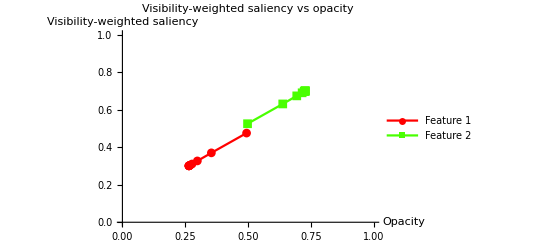

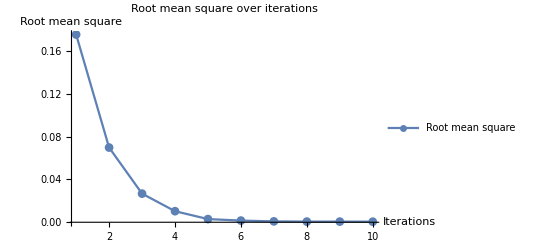

| Visibility-Weighted Saliency | Opacity | Root Mean Square | Steps | Multiplier
1 | 0.475128
0.524872 | 0.494118
0.498039 | 0.175128 | -0.0175128
0.0175128 | 8
2 | 0.369704
0.630296 | 0.354016
0.638141 | 0.0697041 | -0.00697041
0.00697041 | 8
3 | 0.326703
0.673297 | 0.298252
0.693905 | 0.0267031 | -0.00267031
0.00267031 | 8
4 | 0.310319
0.689681 | 0.27689
0.715267 | 0.010319 | -0.0010319
0.0010319 | 8
5 | 0.302959
0.697041 | 0.268635
0.723522 | 0.00295866 | -0.000295866
0.000295866 | 8
6 | 0.301557
0.698443 | 0.266268
0.725889 | 0.001557 | -0.0001557
0.0001557 | 8
7 | 0.300813
0.699187 | 0.265022
0.727135 | 0.000812664 | -0.0000812664
0.0000812664 | 1
8 | 0.300598
0.699402 | 0.264941
0.727216 | 0.000598051 | -0.0000598051
0.0000598051 | 1
9 | 0.300598
0.699402 | 0.264881
0.727276 | 0.000598051 | -0.0000598051
0.0000598051 | 8
10 | 0.300522
0.699478 | 0.264403
0.727754 | 0.000521512 | -0.0000521512
0.0000521512 | 4

```mathematica
t2-t1
iteration
saliency3=ListLinePlot[Transpose[#&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Visibility-weighted saliency over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Visibility-weighted saliency"}]
Export[NotebookDirectory[]<>dataname<>"_saliency_linesearch.png",saliency3];
opacity3=ListLinePlot[Transpose[#2&@@@list],PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotLabel->"Opacity over iterations",PlotRange->{All,{0,1}},PlotStyle->chartcolors,PlotMarkers->Automatic,AxesLabel->{"Iterations","Opacity"}]
Export[NotebookDirectory[]<>dataname<>"_opacity_linesearch.png",opacity3];
x=Transpose[#2&@@@list];
y=Transpose[#&@@@list];
(*ListLinePlot[{Transpose[{x[[1]],y[[1]]}],Transpose[{x[[2]],y[[2]]}],Transpose[{x[[3]],y[[3]]}]},PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]*)
ListLinePlot[Transpose[{x[[#]],y[[#]]}]&/@Range[Length[chartcolors]],PlotStyle->chartcolors,PlotLabel->"Visibility-weighted saliency vs opacity",AxesLabel->{"Opacity","Visibility-weighted saliency"},PlotLegends->{"Feature 1","Feature 2","Feature 3","Feature 4"},PlotRange->{{0,1},{0,1}},PlotMarkers->Automatic]
rms3=ListLinePlot[#3&@@@list,PlotLegends->{"Root mean square"},PlotLabel->"Root mean square over iterations",PlotRange->{All,All},PlotMarkers->Automatic,AxesLabel->{"Iterations","Root mean square"}]
Export[NotebookDirectory[]<>dataname<>"_rms_linesearch.png",rms3];
table3=TableForm[list,TableHeadings->{Automatic,{"Visibility-Weighted Saliency","Opacity", "Root Mean Square","Steps","Multiplier"}},TableSpacing->{2,3}]
Export[NotebookDirectory[]<>dataname<>"_table_linesearch.png",table3];
(*path3=Prepend[#2&@@@list,alpha[[#]]&/@index];*)
path3=#2&@@@list;
AppendTo[records,{t2-t1,iteration,Last[path3]}];
```

```mathematica
recordxml=NotebookDirectory[]<>"~images\\records.xml";
recordmap=If[FileExistsQ[recordxml],Association@Import[recordxml],<||>];
AssociateTo[recordmap,dataname->records];
Export[recordxml,Normal[recordmap]];
dataname->records
```

foot_naive→{{71.635304,37,{0.268669,0.723488}},{17.071891,4,{0.264265,0.727892}},{32.406178,4,{0.264403,0.727754}}}

```mathematica
(*range=Range[0,1,0.1];
coordinates=Flatten[Table[{i,j,k},{i,range},{j,range},{k,range}],2];
Length[coordinates]
Clear[f];
Clear[data];
AbsoluteTiming[
searchspace=ParallelTable[Module[{mean,rms},
mean=VisibilitySaliency[c];
rms=RootMeanSquare[mean-target];
{mean,c,rms}
],{c,coordinates}];
]*)
```

```mathematica
(*transform=RotationTransform[-90 Degree,{0,0,1}];
vec=transform[{1.3, -2.4, 2.}];
opacitylist=#2&@@@searchspace;
rmslist=#3&@@@searchspace;
merged=ParallelTable[Append[opacitylist[[i]],rmslist[[i]]],{i,Length[opacitylist]}];
densityplot=ListDensityPlot3D[merged,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic,PlotLabel->{"x","y","z"},PlotTheme->"Detailed",OpacityFunction->Automatic];
paths={path1,path3};
pathcolors={Red,Green,Blue};
plotlegends={{"Fixed step size"},{"Adaptive step size with line search"},{"Adaptive step size with parallel search"}};
pointplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]],Thick,PointSize[Large]},PlotLegends->plotlegends[[i]]],{i,Length[paths]}];
lineplots=ParallelTable[ListPointPlot3D[paths[[i]],PlotStyle->{pathcolors[[i]]}]/.Point->Line,{i,Length[paths]}];
sp=Show[densityplot,PlotLabel->"Objective function in parameter space",ViewPoint->vec]
sp2=Show[densityplot,pointplots[[1]],pointplots[[2]],lineplots[[1]],lineplots[[2]],PlotLabel->"Gradient descent in parameter space",ViewPoint->vec]
Export[NotebookDirectory[]<>dataname<>"_parameterspace.png",sp];
Export[NotebookDirectory[]<>dataname<>"_parameterspace_path.png",sp2];

{c1,c2,c3}=chartcolors;
blend1=Blend[{{0,Black},{0.5,c1},{1,White}},#]&;
blend2=Blend[{{0,Black},{0.5,c2},{1,White}},#]&;
blend3=Blend[{{0,Black},{0.5,c3},{1,White}},#]&;
saliencylist=#&@@@searchspace;
first=#&@@@saliencylist;
second=#2&@@@saliencylist;
third=#3&@@@saliencylist;
merged1=ParallelTable[Append[opacitylist[[i]],first[[i]]],{i,Length[opacitylist]}];
merged2=ParallelTable[Append[opacitylist[[i]],second[[i]]],{i,Length[opacitylist]}];
merged3=ParallelTable[Append[opacitylist[[i]],third[[i]]],{i,Length[opacitylist]}];
dplots=ListDensityPlot3D[#1,ColorFunction->#2,PlotLegends->Automatic,PlotTheme->"Detailed",OpacityFunction->(#&)]&@@@{{merged1,blend1},{merged2,blend2},{merged3,blend3}};
densityplots=MapIndexed[Show[#,PlotLabel->"Visibility-weighted saliency of feature "<>ToString[First@#2],ViewPoint->vec]&,dplots]
MapIndexed[Export[NotebookDirectory[]<>dataname<>"_densityplot"<>ToString[First@#2]<>".png",#]&,densityplots];*)
```

```mathematica
saveTransferFunction[peaks_,filename_]:=Module[{a2,rgba2,intensity2,rgbafunction2,rgba2denormalized,xrgba,strlist,alphaMode,gammaValue,domain,threshold,k,int,split,colorL,keylist,keys,TransFuncIntensity,VoreenData,xml},
MapIndexed[(alpha0[[#]]=peaks[[First@#2]])&,index0];
a2=IntegerPart[255*alpha0[[#]]]&/@rangeOfAlpha;
rgba2=(#/255.&)/@Transpose[{r,g,b,a2}]//(RGBColor/@#&);
intensity2=intensity0[[#]]&/@rangeOfAlpha;
rgbafunction2=(Blend[Transpose[{intensity2,rgba2}], #] & );(* for return only. not used in this function *)

rgba2denormalized=Transpose[{r,g,b,a2}];
xrgba=Table[Join[{intensity2[[i]]},rgba2denormalized[[i]]],{i,Length[intensity2]}];
strlist={ToString[#1],ToString[#2],ToString[#3],ToString[#4],ToString[#5]}&@@@xrgba;
alphaMode=XMLElement["alphaMode",{"value"->"1"},{}];
gammaValue=XMLElement["gammaValue",{"value"->"1"},{}];
domain=XMLElement["domain",{"x"->"0","y"->"1"},{}];
threshold=XMLElement["threshold",{"x"->"0","y"->"1"},{}];
k=({int=XMLElement["intensity",{"value"->#1},{}],split=XMLElement["split",{"value"->"false"},{}],colorL=XMLElement["colorL",{"r"->#2,"g"->#3,"b"->#4,"a"->#5},{}]}&)@@@strlist;
keylist=XMLElement["key",{"type"->"TransFuncMappingKey"},{#1,#2,#3}]&@@@k;
keys=XMLElement["Keys",{},keylist];
TransFuncIntensity=XMLElement["TransFuncIntensity",{"type"->"TransFuncIntensity"},{alphaMode,gammaValue,domain,threshold,keys}];
VoreenData=XMLElement["VoreenData",{"version"->"1"},{TransFuncIntensity}];
xml=XMLObject["Document"][{XMLObject["Declaration"]["Version"->"1.0"],XMLObject["Comment"]["This is a Voreen transfer function exported from Mathematica"]},VoreenData,{}];
Export[filename,xml, "XML"];
rgbafunction2
];
```

```mathematica
tf1=saveTransferFunction[Last[path1],NotebookDirectory[]<>dataname<>"_optimized_fixed.tfi"];
tf2=saveTransferFunction[Last[path2],NotebookDirectory[]<>dataname<>"_optimized_parallelsearch.tfi"];
tf3=saveTransferFunction[Last[path3],NotebookDirectory[]<>dataname<>"_optimized_linesearch.tfi"];
Image3D[d,ColorFunction->rgbafunction,ViewPoint->viewpoints[face]]
Image3D[d,ColorFunction->tf3,ViewPoint->viewpoints[face]]
ListLinePlot[Transpose[{intensity,alpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"Before optimization"]
(*Transpose[{intensity,r,g,b,a}]*)
ListLinePlot[Transpose[{intensity0[[#]]&/@rangeOfAlpha,alpha0[[#]]&/@rangeOfAlpha}],PlotRange->{{0,1},{0,1}},ColorFunction->rgbfunction,PlotLegends->"After optimization"]
(*xrgba*)
```

-Graphics-

-Graphics-